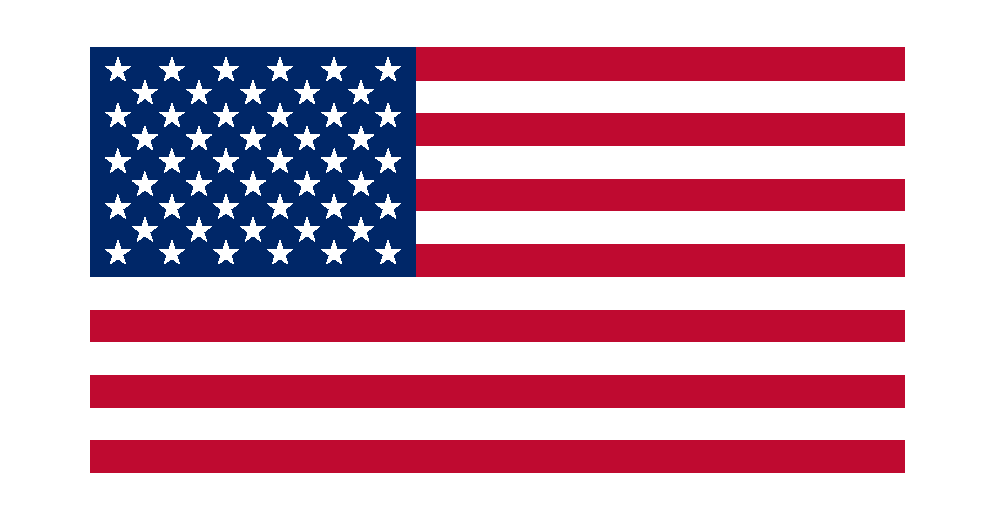

```mathematica
MyBlue=RGBColor[0/255,39/255,104/255];
MyRed=RGBColor[191/255,10/255,48/255];
MyWhite=RGBColor[255/255,255/255,255/255];
MyBlack=RGBColor[0,0,0];

w=1;
h=w/1.91;
f=h*7*Sqrt[2]/13;
s=h*(GoldenRatio-1)/20;

MyStar[x_:0,y_:0,r_:1]:=Polygon[Flatten[Table[{r*{Cos[2*Pi*k/5+Pi/2],Sin[2*Pi*k/5+Pi/2]}+{x,y},r/(1+GoldenRatio)*{Cos[2*Pi*k/5+Pi/2+Pi/5],Sin[2*Pi*k/5+Pi/2+Pi/5]}+{x,y}},{k,0,4}],1]]

Stripes=Flatten[Table[{If[EvenQ[i],MyRed,MyWhite],Rectangle[{0,i*h/13},{w,(i+1)*h/13}]},{i,0,12}]];
Field={MyBlue,Rectangle[{0,h*6/13},{f,h}]};
Stars=Prepend[Join[Flatten[Table[MyStar[j*f/12,h-i*h*7/130,s],{i,1,9,2},{j,1,11,2}]],Flatten[Table[MyStar[j*f/6,h-i*h*7/65,s],{i,4},{j,5}]]],MyWhite];
Graphics[Join[Stripes,Field,Stars]]
```